```mathematica
data = Import["output.csv"]
```

{{Time / ns,TotEng / Kcal mole⁻.b9,KinEng / Kcal mole⁻.b9,PotEng / Kcal mole⁻.b9,Enthalpy / Kcal mole⁻.b9,Temp / K,Press / atm,Volume / Å.b3,Density / g cm⁻.b9},30002,{150.125,-32619.9,1814.73,-34434.6,-33004.5,203.002,-285.62,92345.4,0.971828}}
 |  |  |  |

```mathematica
blue = RGBColor[21/256,109/256,204/256];
red = RGBColor[255/256,64/256,49/256];
green = RGBColor[0/256,163/256,55/256];
yellow = RGBColor[1.,0.62,0.19];
purple = RGBColor[1.,0.89,0.81];
purple = RGBColor[0.62,0.63,1.];
```

```mathematica
t = Transpose[data][[1]];
te = Transpose[data][[2]];
ke = Transpose[data][[3]];
pe = Transpose[data][[4]];
en = Transpose[data][[5]];
tp = Transpose[data][[6]];
pr = Transpose[data][[7]];
vo = Transpose[data][[8]];
de = Transpose[data][[9]];
```

```mathematica
rte = Partition[Riffle[t, te], 2];
rke = Partition[Riffle[t, ke], 2];
rpe = Partition[Riffle[t, pe], 2];
ren = Partition[Riffle[t, en], 2];
rtp = Partition[Riffle[t, tp], 2];
rpr = Partition[Riffle[t, pr], 2];
rvo = Partition[Riffle[t, vo], 2];
rde = Partition[Riffle[t, de], 2];
```

```mathematica
marte = MovingAverage[Rest[rte], 1000];
marke = MovingAverage[Rest[rke], 1000];
marpe = MovingAverage[Rest[rpe], 1000];
maren = MovingAverage[Rest[ren], 1000];
martp = MovingAverage[Rest[rtp], 1000];
marpr = MovingAverage[Rest[rpr], 1000];
marvo = MovingAverage[Rest[rvo], 1000];
marde = MovingAverage[Rest[rde], 1000];
```

## Temp

## Raw data Temp

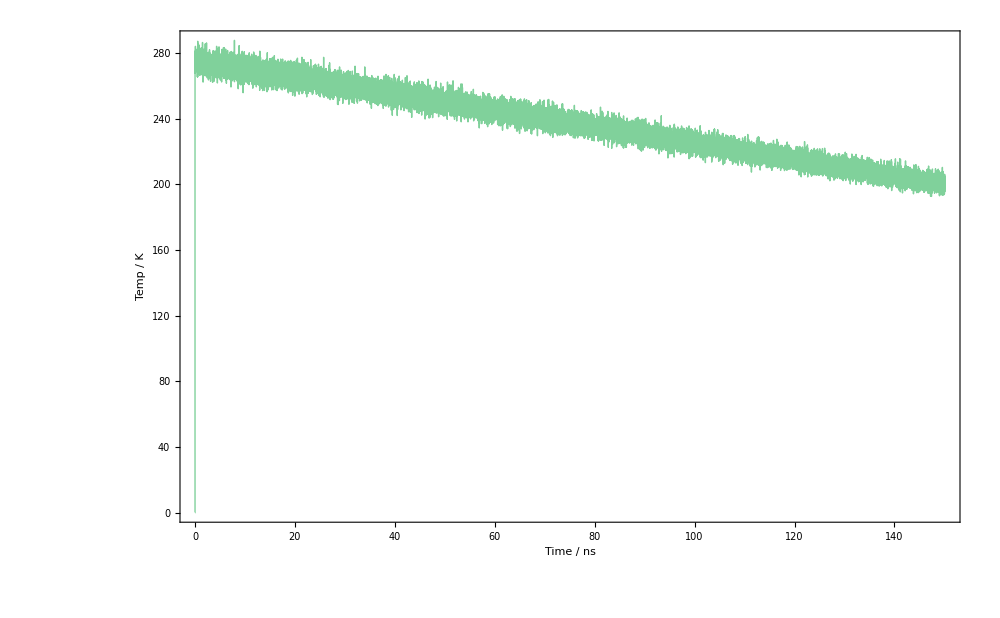

```mathematica
ListPlot[
rtp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]
```

## Moving average temp

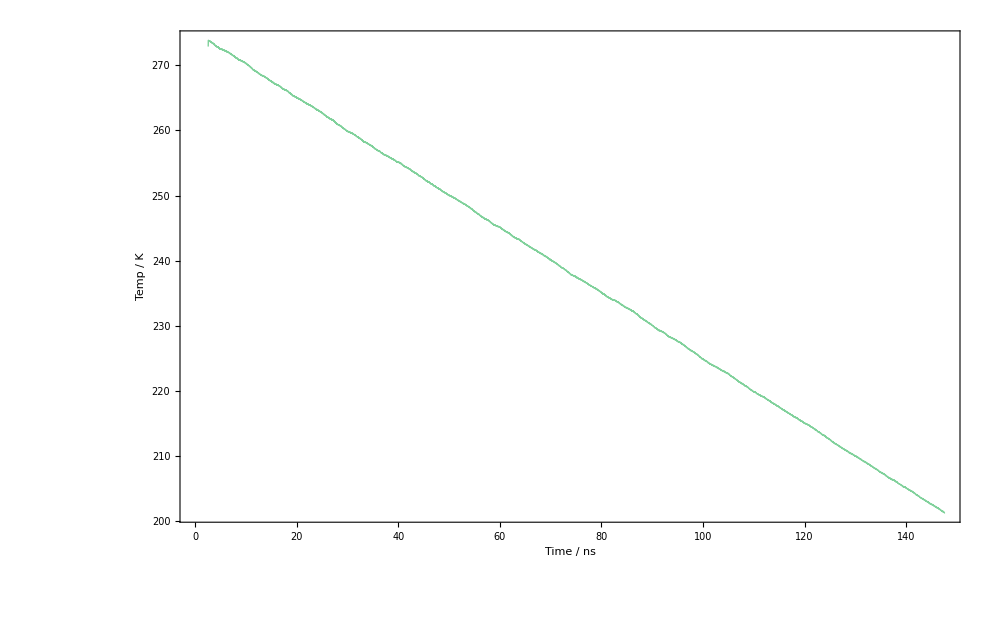

```mathematica
ListPlot[
martp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]
```

## Moving average temp from 130 -> 145 ns

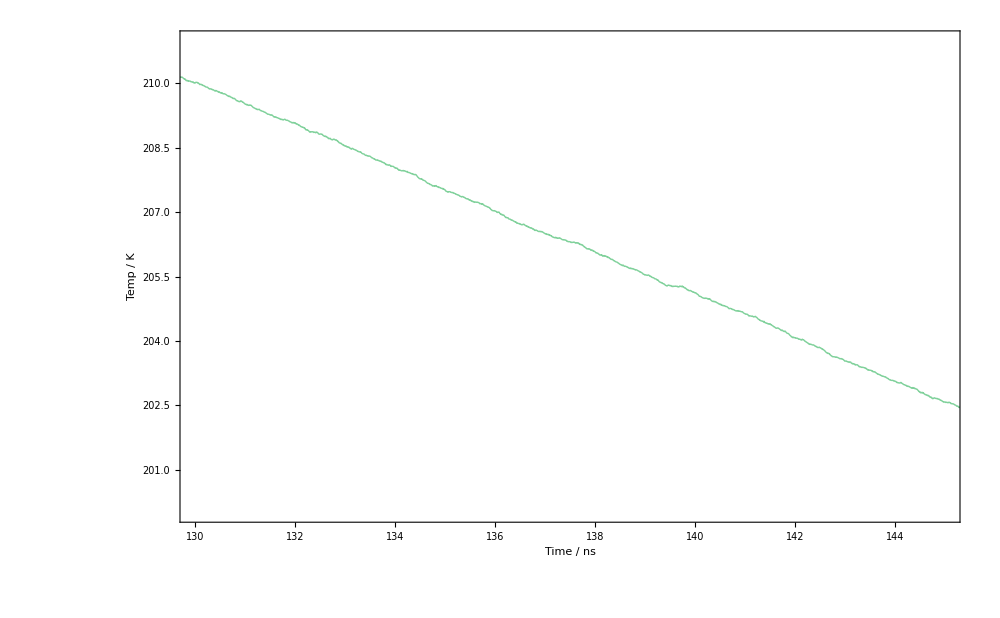

```mathematica
ListPlot[
martp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {200, 211}}
]
```

## Pressure

## Raw data Press

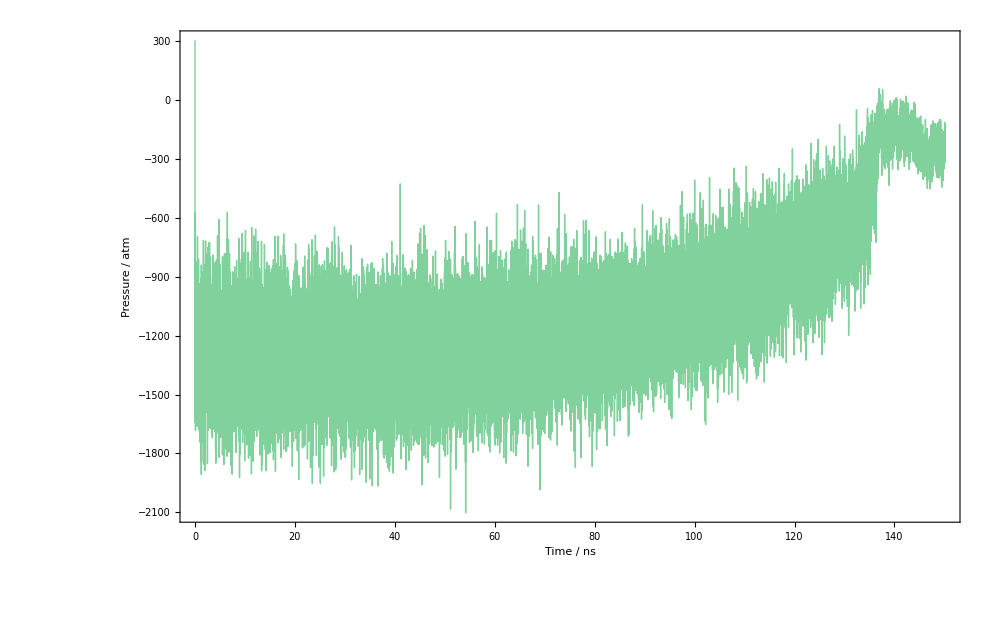

```mathematica
ListPlot[
rpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]
```

## Moving average Press between 120 -> 150 ns

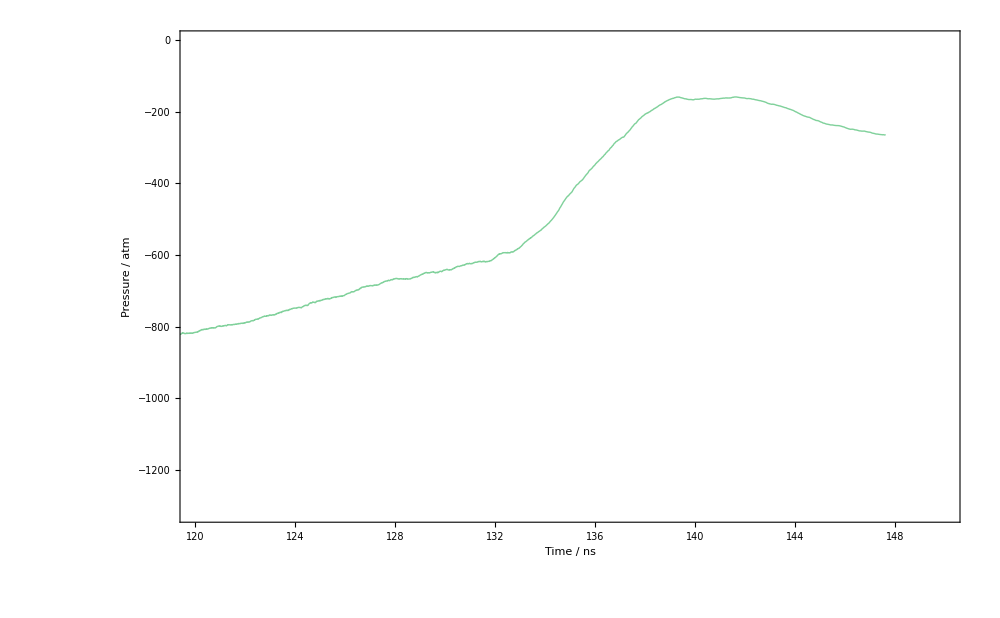

```mathematica
ListPlot[
marpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{120, 150}, Automatic}
]
```

## Moving average Press between 130 -> 145 ns

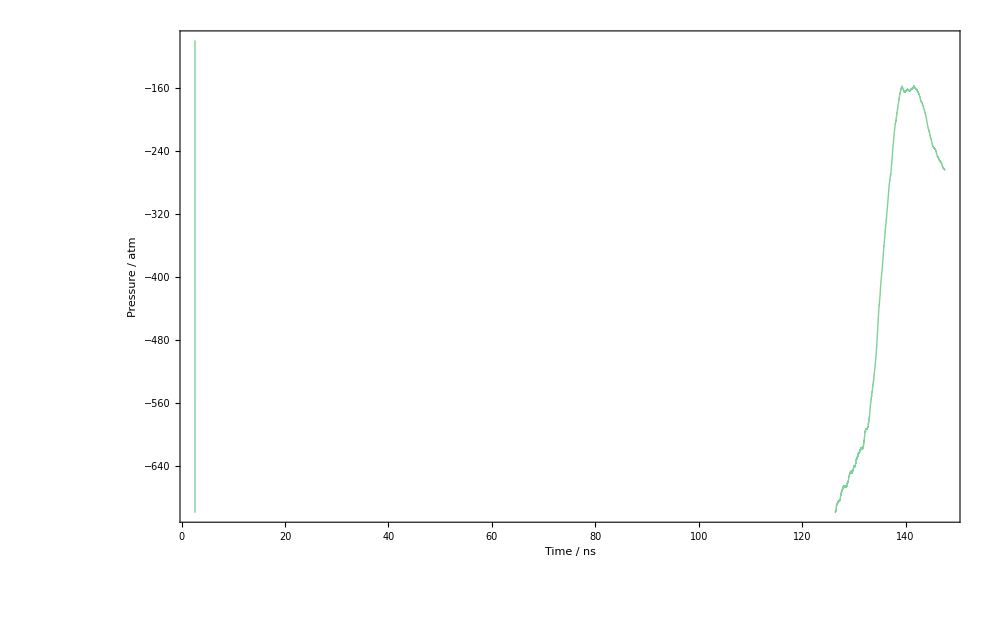

```mathematica
ListPlot[
marpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {-100, -700}}
]
```

## Energies

## Moving averages of TE, KE, PE, EN v time

```mathematica
ListPlot[
{ marte, marke, marpe, maren}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,blue}, 

{Thick,Dashed,Lighter[blue,0.5]}, 

{Thick,red}, 

{Thick,green}
},
PlotLabels->{"TE", "KE", "PE", "Enthalpy"},
ImageSize -> {1000,700}
]
```

-Graphics-

## Moving averages of TE, KE, PE, EN from 120 -> 150 ns

```mathematica
ListPlot[
{ marte, marke, marpe, maren}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,blue}, 

{Thick,Dashed,Lighter[blue,0.5]}, 

{Thick,red}, 

{Thick,green}
},
PlotLabels->{"TE", "KE", "PE", "Enthalpy"},
ImageSize -> {1000,700},
PlotRange->{{120, 150}, Automatic}
]
```

-Graphics-

## Moving averages of TE, Enthalpy, PE

```mathematica
ListPlot[
{ marte, maren, marpe}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green},
{Thick, blue}
},
PlotLabels->{"TE","Enthalpy", "PE"},
ImageSize -> {1000,700}
]
```

-Graphics-

## Moving averages of TE, Enthalpy, PE from 120 -> 150ns

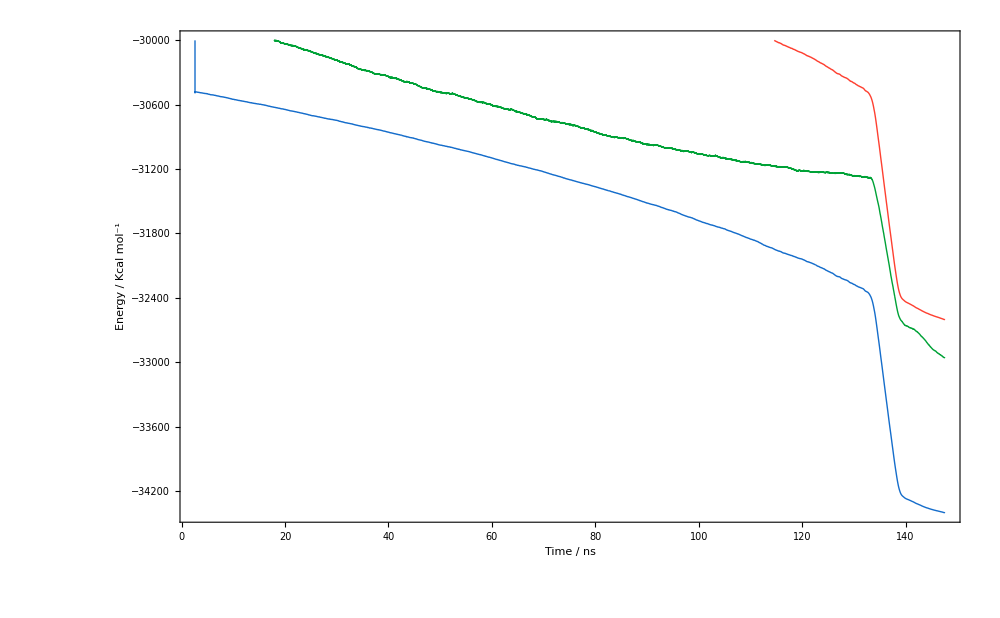

```mathematica
ListPlot[
{ marte, maren, marpe}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green},
{Thick, blue}
},
PlotLabels->{"TE","Enthalpy", "PE"},
ImageSize -> {1000,700},
PlotRange->{{120, 150}, {-30000, -34500}}
]
```

## Moving averages of TE, Enthalpy, PE from 130 -> 145ns

```mathematica
ListPlot[
{ marte, maren, marpe}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green},
{Thick, blue}
},
PlotLabels->{"TE","Enthalpy", "PE"},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {-30000, -34500}}
]
```

-Graphics-

## Combinations

## Enthalpy + Press form 130 -> 145 ns

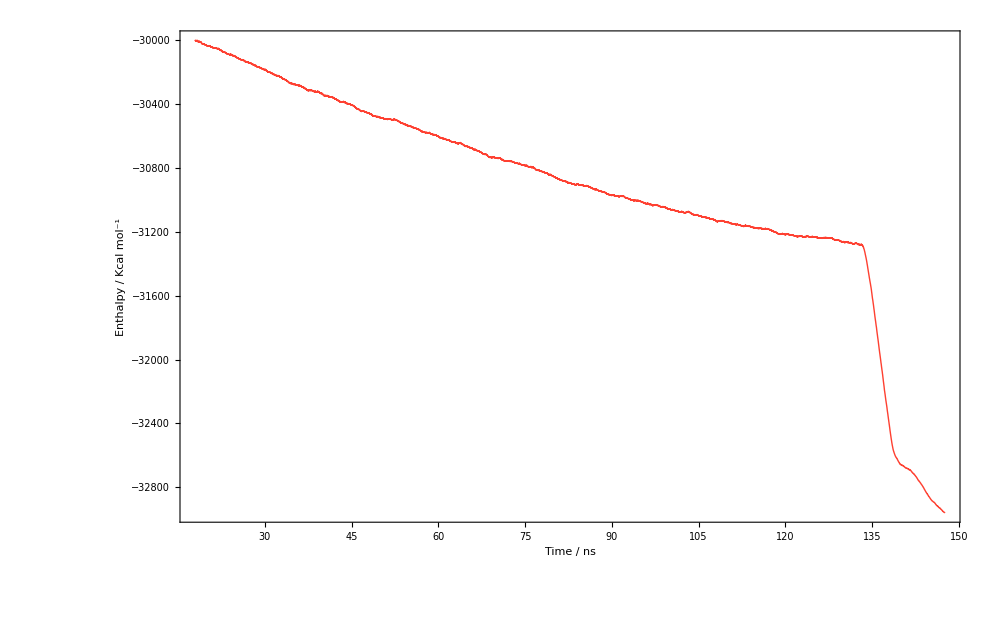
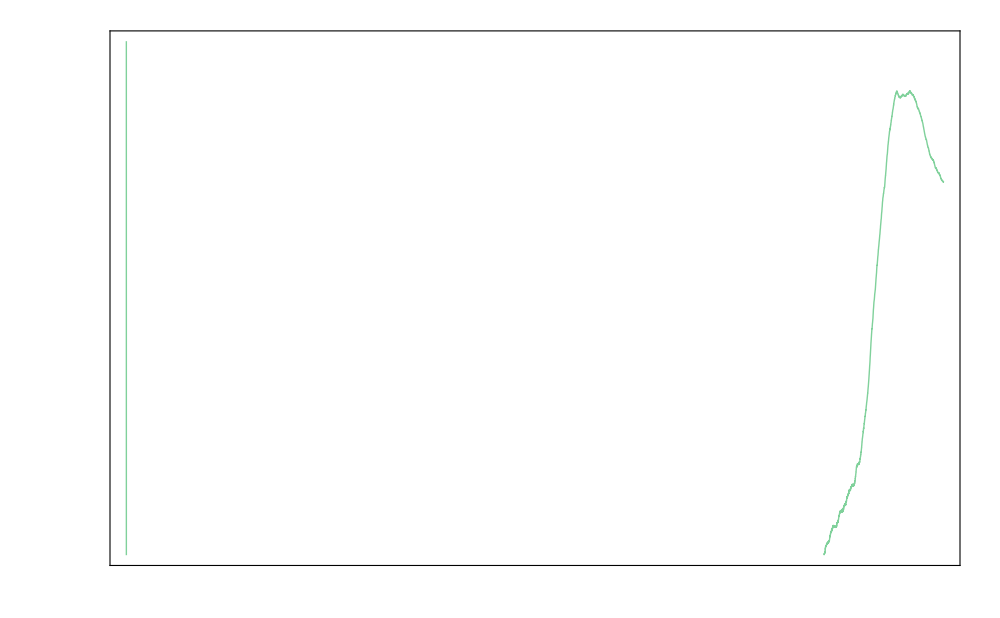

```mathematica
en130145 = ListPlot[
maren, 
Joined->True,
FrameLabel->{"Time / ns", "Enthalpy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> {Thick,red},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {-30000, -34500}},
ImagePadding->110,
Frame->{True,True,True,False},
FrameTicks->{All, All, All, None},
FrameStyle->{Automatic,red,Automatic,Automatic}
];
p130145 = ListPlot[
marpr,
Joined->True,
FrameLabel->{{None, "Pressure / atm"}, {None, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {-100, -700}},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
FrameStyle->{Automatic,Automatic,Automatic,green},
ImagePadding->110
];
Overlay[{en130145, p130145}]
```

## Enthalpy + Temp from 130 -> 145ns

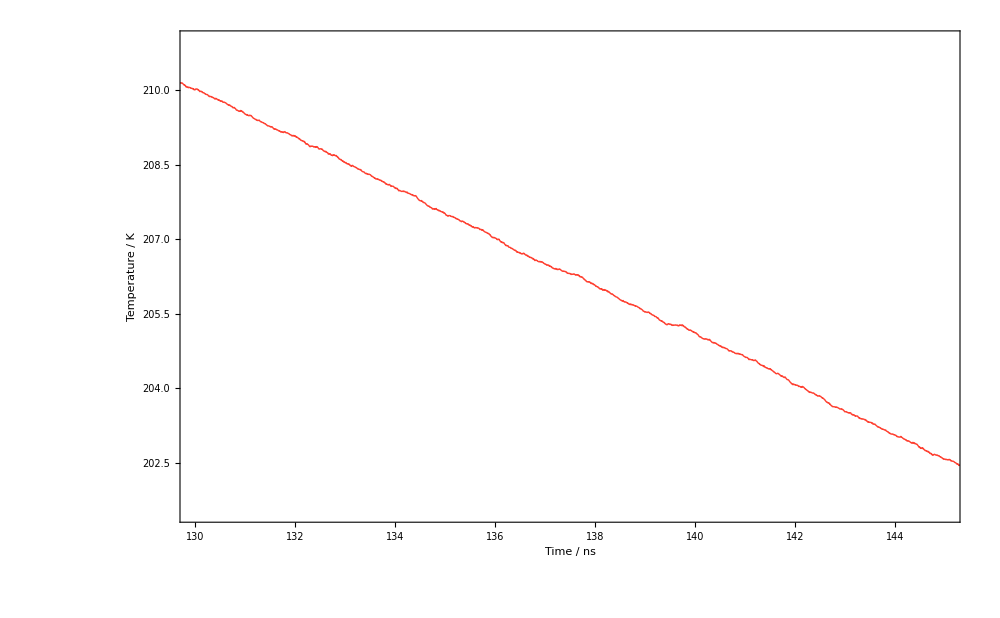
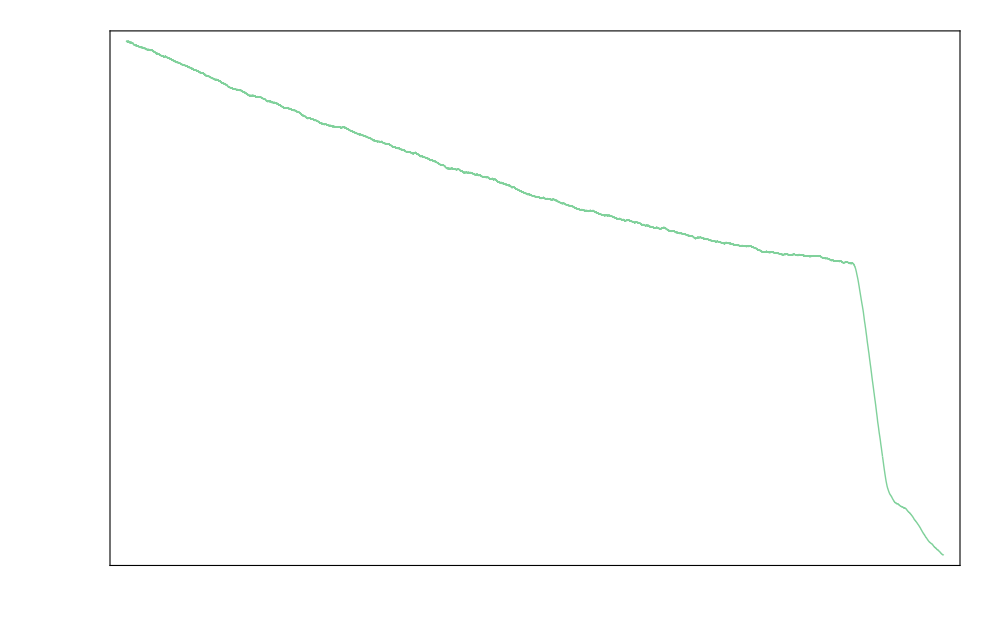

```mathematica
tp130145 = ListPlot[
martp, 
Joined->True,
FrameLabel->{"Time / ns", "Temperature / K"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> {Thick,red},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {201.5, 211}},
ImagePadding->110,
Frame->{True,True,True,False},
FrameTicks->{All, All, All, None},
FrameStyle->{Automatic,red,Automatic,Automatic}
];
p130145 = ListPlot[
maren,
Joined->True,
FrameLabel->{{None, "Enthalpy / Kcal mol^-1"}, {None, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{130, 145}, {-30000, -34500}},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
FrameStyle->{Automatic,Automatic,Automatic,green},
ImagePadding->110
];
Overlay[{tp130145, p130145}]
```